# Teoría de Autómatas y Lenguajes Formales

## Clase 9: Gramáticas Libres (Independientes) de Contexto

Profesor: Tomás de Camino Beck, Ph.D.

## Introducción

Las gramáticas independientes de contexto  (GIC),  se definen:

Conjunto finito de símbolos  que se les llaman símbolos terminales

Conjunto de variables  (símbolos no terminales o categorías sintácticas)

Variable inicial

Reglas de producción  de la forma , donde

## GIC en Mathematica

En Mathematica podemos utilizar la estructura de Rules parte del lenguajes.  Hay varias formas de trabajarlo, y una es utilizar textos para construir GIC.

### Definición de reglas de producción

Basado en el ejemplo de Hopcroft de la figura 5.1 (pg. 145), definimos las reglas de producción para un palíndromo,

```mathematica
rules= {
"P"->"",
"P"->"0",
"P"-> "1",
"P"-> "0P0",
"P"-> "1P1"
}
```

{P→,P→0,P→1,P→0P0,P→1P1}

Ahora podemos construir una función que deriva a partir de una variable inicial, las producciones posibles.

### Construyendo una función de Producción

Utilizamos la función StringReplace para aplicar las reglas a un string inicial,

```mathematica
StringReplaceList[{"P","0P0"},rules]
```

{{,0,1,0P0,1P1},{00,000,010,00P00,01P10}}

Luego aplicamos de forma recursiva utilizando NestList,

```mathematica
NestList[StringReplaceList[#,rules]&,"P",2]/.{}->Nothing
```

{P,{,0,1,0P0,1P1},{{00,000,010,00P00,01P10},{11,101,111,10P01,11P11}}}

Ahora podemos construir una función general que nos permita aplicarlos a cualquier GIC,

```mathematica
ProductionRule[s0_,rules_,n_]:=Union[Flatten[NestList[Flatten[StringReplaceList[#,rules]]&,s0,n]]]
```

Del ejemplo de palíndromos, hacemos 4 iteraciones

```mathematica
rp=ProductionRule["P",rules,4]
```

{,0,00,000,0000,00000,000000,0000000,0000P0000,0001000,0001P1000,000P000,00100,0010100,0010P0100,001100,0011100,0011P1100,001P100,00P00,010,0100010,010010,0100P0010,01010,0101010,0101P1010,010P010,0110,0110110,0110P0110,01110,011110,0111110,0111P1110,011P110,01P10,0P0,1,1000001,100001,10001,1000P0001,1001,1001001,1001P1001,100P001,101,10101,1010101,1010P0101,101101,1011101,1011P1101,101P101,10P01,11,1100011,110011,1100P0011,1101011,11011,1101P1011,110P011,111,1110111,1110P0111,1111,11111,111111,1111111,1111P1111,111P111,11P11,1P1,P}

### Representación visual de las reglas

Para facilitar la visualización, podemos utilizar ArrayPlot para graficar las producciones de una GIC,

```mathematica
PlotStrings[l_List,opts___]:=Map[ArrayPlot[{Characters[#]},opts]&,l]
```

Aplicado al ejemplo de los palíndromos,

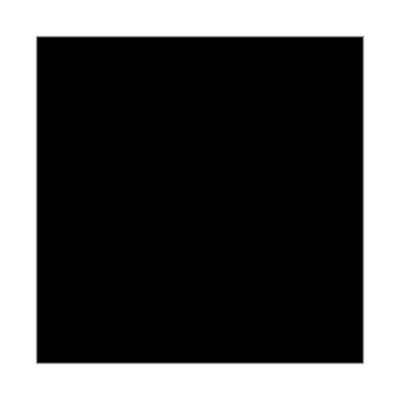
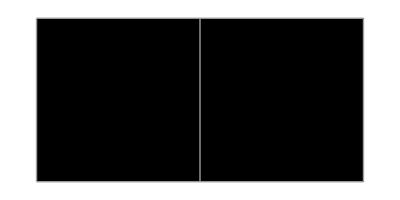
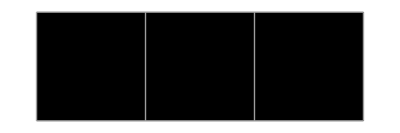
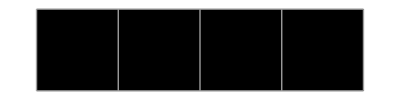
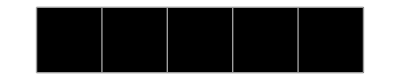
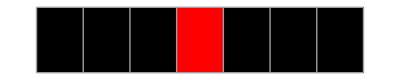
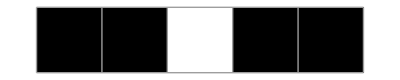
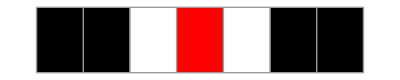

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotStrings[ProductionRule["P",rules,3],ColorRules->{"1"->White,"0"->Black,"P"->Red},Mesh->All,ImageSize->{Automatic,30}]
```

## Validar un string

Utilizando la función de PruductionRule construida, podemos ahora verificar si un string pertenece al conjunto creado por las producción

```mathematica
IsValidQ[string_,s0_,rules_]:=MemberQ[ProductionRule[s0,rules,StringLength[string]],string]
```

Por ejemplo evaluar si 001100 es un palíndromo,

```mathematica
IsValidQ["001100","P",rules]
```

True

Esta forma de validar un string es poco eficiente, ya que construye todas las producciones posibles, y esto aumenta de forma considerable dependiendo de las reglas de producción, vean el tiempo de ejecución dependiendo del número de iteraciones de producción,

```mathematica
et=Table[First[AbsoluteTiming[ProductionRule["P", rules, i]]],{i,15}];
```

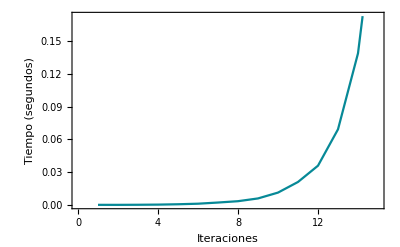

```mathematica
ListLinePlot[et,Frame->True,FrameLabel->{"Iteraciones","Tiempo (segundos)"}]
```

El tiempo de ejecución es exponencial por tanto, es poco práctico como método de evaluación.

## Ejemplos adicionales

### Ejemplo 5.3 Hopcroft (pagina 146)

```mathematica
rules={
"E"-> "I",
"E"-> "E+E",
"E"-> "(E)",
"I"->"a",
"I"->"b",
"I"->"Ia",
"I"->"Ib",
"I"->"I0",
"I"->"I1"
}
```

{E→I,E→E+E,E→(E),I→a,I→b,I→Ia,I→Ib,I→I0,I→I1}

```mathematica
ProductionRule["E",rules,2]
```

{a,b,Ia,Ib,I0,I1,I+E,E+E+E,(E)+E,E+I,E+E+E,E+(E),(I),(E+E),((E))}

## Reto

Utilizar derivación o inferencia para determinar si una producción es válida.

## Funciones utilizadas

StringReplacepaclet:ref/StringReplace["string",s→sp]
replaces the string expression s by sp wherever it appears in "string".

NestListpaclet:ref/NestList[f,expr,n]
gives a list of the results of applying f to expr 0 through n times.

Flattenpaclet:ref/Flatten[list]
flattens out nested lists.

Characterspaclet:ref/Characters["string"]
gives a list of the characters in a string.

ArrayPlotpaclet:ref/ArrayPlot[array]
generates a plot in which the values in an array are shown in a discrete array of squares.

| GraphicsGridpaclet:ref/GraphicsGrid[{{g_11,g_12,…},…}]
generates a graphic in which the g_ij are laid out in a two-dimensional grid.

| ListLinePlotpaclet:ref/ListLinePlot[{y_1,y_2,…}]
plots a line through the points {1,y_1},{2,y_2},….

AbsoluteTimingpaclet:ref/AbsoluteTiming[expr]
evaluates expr, returning a list of the absolute number of seconds in real time that have elapsed, together with the result obtained.